```mathematica
Today
```

Fri 27 Apr 2018

# Solving problems with propositional logic

Mechanical computers are really nothing more complicated than very high speed machines that perform elementary logical operations on zeros and ones. Higher level concepts and their operations such as integers and their arithmetic are built up from these basic logical operations implemented in the computer hardware, and these concepts are then used to build higher abstraction structures and superstructures. But deep down, all computation boils down to zeros and ones and the elementary operations to use them to produce more zeros and ones.
A fundamental result from the theory of computational complexity says that all computational problems that can be solved in practical time can be mechanistically converted to a set of propositional variables and a corresponding set of logical clauses that constrain the possible value combinations of those variables, so that these clauses all together are satisfiable if and only if the original problem has a solution. This construction will then allow us to reconstruct the solution of the original problem from the truth values of the propositions of the corresponding satisfiability problem. With modern satisfiability solvers, it is often actually easier and even more efficient to solve problems by converting them to propositional logic instead of trying to implement the backtracking algorithm and think up to the dependencies inside the problem that can be used to guide this search, since we can just let the satisfiability solver implicitly discover these dependencies.
Sudoku puzzles are established enough so that they no longer need their rules explained every time a new instance is printed in the daily newspaper. Here is one possible sudoku found online, described on that web page as being quite difficult for human solvers.

```mathematica
sudokuBoard={
{0,2,0,0,0,0,0,0,0},
{0,0,0,6,0,0,0,0,3},
{0,7,4,0,8,0,0,0,0},
{0,0,0,0,0,3,0,0,2},
{0,8,0,0,4,0,0,1,0},
{6,0,0,5,0,0,0,0,0},
{0,0,0,0,1,0,7,8,0},
{5,0,0,0,0,9,0,0,0},
{0,0,0,0,0,0,0,4,0}
};
```

An n-by-n sudoku where each tile must be filled with one of the n possible values can be encoded as n^3 propositions to express the claims of the form “The tile in coordinates (x, y) has the value v” with x, y and v each going through the integers 1 to n. For the ordinary 9-by-9 Sudoku, this creates a system of 729 propositional logic variables. The rules of Sudoku then enforce a bunch of logical clauses to express constraints that say that whenever the tile has a particular value, then no other tile in the same row, column or box is allowed to have that same value. Furthermore, we must also remember to write constraint clauses that say that each tile must have some value, so that this problem could not be trivially “solved” by refraining from giving its tiles any values at all, which would be within the rules  of the previous constraintsm but not in their spirit. A mindless program trying to solve a problem has no concept of what we finger-quotes “intended” when defining that problem, so the constraint clauses must really explicitly say everything that is allowed and not allowed. (An artificial intelligence may always find surprising lateral thinking solutions for any optimization problems that we give it.)
We start by defining the tiles as list of pairs of the form (x, y), followed by a utility function sameBox that checks whether two tiles are inside the same box.

```mathematica
tiles=Flatten[Table[{x,y},{x,1,9},{y,1,9}],1];
sameBox[{x1_,y1_},{x2_,y2_}]:=Floor[(x1-1)/3]==Floor[(x2-1)/3]&&Floor[(y1-1)/3]==Floor[(y2-1)/3];
```

Two tiles are neighbours if they reside either in the same row, in the same column, or inside the same 3-by-3 square called a box. These three tables are straightforward to generate, after which Union combines them into one list with the duplicate elements removed. From this union, the last thing we have to remember to do is to remove that tile itself. Mathematica list filtering functions Select and DeleteCases (the latter one used in the function sudokuNeighbour defined below to eliminate the tile (x, y) from the list of its neighbours) are useful for this sort of construction of lists whose values should not contains duplicates. In any 9-by-9 Sudoku, each individual tile has exactly 20 neighbours, no more and no less, which will then produce that same number of separate implication clauses that prevent these neighbours from also having the value that was used to fill in this tile.

```mathematica
sudokuNeighbour[{x_,y_}]:=DeleteCases[
Union[
Table[{k,y},{k,1,9}],
Table[{x,k},{k,1,9}],
Select[tiles,(sameBox[#,{x,y}])&]
],{x,y}
];
sudokuNeighbour[{2,2}]
```

{{1,1},{1,2},{1,3},{2,1},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,1},{3,2},{3,3},{4,2},{5,2},{6,2},{7,2},{8,2},{9,2}}

Unlike predicate logic and higher order logics all the way up to our natural language, propositional logic does not allow us to express global constraints such as “If a tile has value v, then none of its neighbours can have the value v” in one swoop. Instead, a separate clause has to be added for every single individual tile on the board, as silly and redundant as this might initially seem. For this reason, whenever interesting computational problems are encoded as sets of propositional logic formulas, they will typically explode into thousands or even millions of propositional variables, so we cannot just use the letters A, B, C, ... to denote these propositions the way that this is conventionally done in the introductory logic textbooks. Instead, most satisfiability solvers simply number these propositions with positive integers 1, 2, 3, ...
With the fully symbolic nature of Mathematica, we can avoid the pointless step of computing which one of these linear numbers would represent the three-dimensional proposition “Tile (x, y) contains the value v” defined by three parameters, since we can simply directly define the propositional variables to be symbolic expressions that carry these three subscripts within that expression. The function sudokuLiteral builds up such symbols that we can then use to build up the clauses to represent the constrains between values of neighbouring tiles.

```mathematica
sudokuLiteral[{x_,y_},v_]:=Subscript[s,{x,y,v}];
sudokuLiteral[{2,2}, 7]
```

s_{2,2,7}

The function sudokuConstraint now produces the constraint clause for the two tiles and value v given to it as parameters.

```mathematica
sudokuConstraint[t1_,t2_,v_]:=
Implies[sudokuLiteral[t1,v],Not[sudokuLiteral[t2,v]]];
sudokuConstraint[{2,2},{3,3},7]
```

s_{2,2,7}⇒!s_{3,3,7}

Before building up the entire set of clauses that the solution to the Sudoku problem must satisfy to qualify as a legal solution, let us take a sidebar to demonstrate the fully symbolic nature of  Mathematica. During computation, everything is an expression and kept as such, to be simplified by the Mathematica’s powerful pattern matching engine only when needed. Literal values such as 42 are simply special cases of arbitrary expressions that will then not simplify any further. Even though we usually think of Length and Part and similar operations specifically as list operations, in Mathematica they are actually operations on arbitrary expressions, of which lists are just a special case. Each expression is a tree structure that consists of a head that determines the dynamic type of the expression, combined with some number of arguments (internally converted to the canonical sorted form) that we can extract with Part, usually abbreviated with the [[ ]] notation.

```mathematica
example1 = {42, hello, foo + bar};
example2 = zup[42, hello, foo + bar];
{Head[example1],example1[[3]], Head[example2], example2[[3]]}
```

{List,bar+foo,zup,bar+foo}

For practical reasons, lists are defined to be special in Mathematica in that many built-in functions are defined to have the attribute Listable so that the pattern matching engine can automatically apply them to the elements of a list. Whenever you define your own function foo, you can make it similarly listable by saying SetAttributes[foo, Listable], after which Mathematica can automatically thread it over list arguments.

```mathematica
Sin[{2, π/2, foo + bar}]
```

{Sin[2],1,Sin[bar+foo]}

Because Mathematica has such powerful functions to produce specifically lists, many other expressions are much easier to build up piecemeal by building up their structure as a nested lists, of which we then replace the head with a different, more desirable head to turn that expression into an expression that is not a list. The function Apply can take any expression and replace its Head with an arbitrary symbol. This allows us to build a complex expression with the list processing functions, and then use Apply to to turn the list into the desired expression. Like all frequently used Mathematica functions, Apply has a common shorthard form @@. In the next example, items is defined to be a list, but then turned into the sum of its elements with simple replacement of its head.

```mathematica
items = {2, 5, nicedoggie/ Cos[2]};
Plus @@ items
```

7+nicedoggie Sec[2]

The logical formula that enforces the constraints between the tiles in the Sudoku board is a giant logical conjunction between these individual clauses, since all of these formulas must be simultaneously true for the solution to be legal. Each clause is itself a logical conjunction of the implicative constraints between the tile and its neighbours, and the logical disjunction of the possible nine values for that particular tile to enforce that each tile must have some value filled in it. For the tiles that are given a fixed value in the problem specification, the clauses for that tile consist of only the one literal that says that the tile must have that very value in the solution. The clauses for the neighbours of this tiles enforce that their values will not contradict the given fixed value for this tile.

```mathematica
sudokuClauses[{x_,y_}]:=If[sudokuBoard[[x,y]]>0,
sudokuLiteral[{x,y},sudokuBoard[[x,y]]]
,(*else*)
And[
Or@@Table[sudokuLiteral[{x,y},v],{v,1,9}],
And@@Table[And@@
Table[sudokuConstraint[{x,y},n,v],{n,sudokuNeighbour[{x,y}]}],{v,1,9}]]];

sudokuProblem=And@@Flatten[Table[sudokuClauses[{x,y}],{x,1,9},{y,1,9}],1];
```

As expected, the problem encoding to propositional logic produces quite a few individual clauses. Using the well-known conversion to the standard conjunctive normal form, the number of clauses decreases quite a bit. The exact number of clauses depends on the complexity of the particular Sudoku instance; the more tiles the problem already gives the value to, the fewer constraints those tiles add to the entire problem, making that problem easier to solve when the search has fewer available alternatives to fill in the value of the next tile. This seems intuitively obvious.

```mathematica
Length[sudokuProblem]
Length[BooleanConvert[sudokuProblem, "CNF"]]
```

11241

7056

Having built up the clauses to define the problem, we can now solve it with Mathematica’s built-in satisfiability solver, trusting its variation of the classic DPLL algorithm to utilize the best known variable ordering and other heuristics during its backtracking search that tries out the value combinations of propositions. Given the problem and the list of propositional variables to solve, the function SatisfiabilityInstances generates one solution that satisfy the problem. This function receives a propositional logic formula without any information about the semantic meaning of those propositions. Being agnostic to the high level details of the problem described in these formulas, the function just twiddles the low level propositions until it finds some working solution, and by doing so, solves the high level problem. (In some problems, useful high level details stemming from symmetry of the problem can be supplied as part of the formula as additional helper clauses that further restrict and prune the search space, which allows the solution then to be discovered faster.)
Since we know that every properly constructed Sudoku problem has exactly one solution, we can unconditionally extract this solution as the first element of the solution list. The Table function is then used to construct the propositions as a three-dimensional structure that we Flatten down to one dimension.

```mathematica
sudokuVars=Flatten[Table[sudokuLiteral[{x,y},v],{x,1,9},{y,1,9},{v,1,9}],2];
solution=First[SatisfiabilityInstances[sudokuProblem,sudokuVars]];
```

The returned solution is a list of 729 truth values for the 729 propositions listed in the same order that those propositions appear in the list sudokuVars. Exactly 81 of these propositions should be True, since every Sudoku tile must be given exactly one value. We can verify that as a quick sanity check to ensure that the computation we have performed so far makes at least a modicum of sense.

```mathematica
Length[Cases[solution, True]]
```

81

Given two lists sudokuVars and solution of the same length, how can we select precisely those elements of sudokuVars where the element of the corresponding position of solution is True? The first way uses the canonical trick of Mathematica to “zip” two lists into a single list that consists of pairs of elements by transposing the matrix that has these lists as rows. From these pairs, we extract those whose second element is True, and then Map the function First over this list of true propositions to extract those propositions.

```mathematica
sollit = Map[First, Cases[Transpose[{sudokuVars, solution}], {x_, True}]]
```

{s_{1,1,1},s_{1,2,2},s_{1,3,6},s_{1,4,4},s_{1,5,3},s_{1,6,7},s_{1,7,9},s_{1,8,5},s_{1,9,8},s_{2,1,8},s_{2,2,9},s_{2,3,5},s_{2,4,6},s_{2,5,2},s_{2,6,1},s_{2,7,4},s_{2,8,7},s_{2,9,3},s_{3,1,3},s_{3,2,7},s_{3,3,4},s_{3,4,9},s_{3,5,8},s_{3,6,5},s_{3,7,1},s_{3,8,2},s_{3,9,6},s_{4,1,4},s_{4,2,5},s_{4,3,7},s_{4,4,1},s_{4,5,9},s_{4,6,3},s_{4,7,8},s_{4,8,6},s_{4,9,2},s_{5,1,9},s_{5,2,8},s_{5,3,3},s_{5,4,2},s_{5,5,4},s_{5,6,6},s_{5,7,5},s_{5,8,1},s_{5,9,7},s_{6,1,6},s_{6,2,1},s_{6,3,2},s_{6,4,5},s_{6,5,7},s_{6,6,8},s_{6,7,3},s_{6,8,9},s_{6,9,4},s_{7,1,2},s_{7,2,6},s_{7,3,9},s_{7,4,3},s_{7,5,1},s_{7,6,4},s_{7,7,7},s_{7,8,8},s_{7,9,5},s_{8,1,5},s_{8,2,4},s_{8,3,8},s_{8,4,7},s_{8,5,6},s_{8,6,9},s_{8,7,2},s_{8,8,3},s_{8,9,1},s_{9,1,7},s_{9,2,3},s_{9,3,1},s_{9,4,8},s_{9,5,5},s_{9,6,2},s_{9,7,6},s_{9,8,4},s_{9,9,9}}

With a little bit of squinting, we could already read the answer from there. But since we have all this computational power in our fingertips, we might as well display the answer in a graphical format more friendly to humans. So, let us define a function to convert the given propositional symbol to a display tile in the graphical display so that the coordinates (x, y) in the subscript of the proposition symbol determine its position on the display, and the value v in the subscript determines the number to show in that position. To make the display seem more whimsical and hand-made, the number shown inside the tile is rotated around its center point by a small random angle left or right.

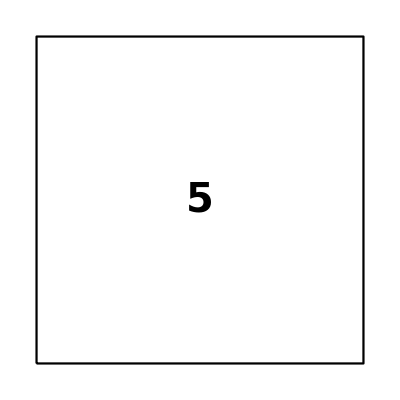

```mathematica
sh[Subscript[s,{x_,y_,v_}]]:={
Thickness[.004],
Background -> White,
Line[{{y-.45,10-x-.45},{y-.45,10-x+.45}, {y+.45,10-x+.45},{y+.45,10-x-.45},{y-.45,10-x-.45}}],
Rotate[Text[Style[v,FontSize->40, FontWeight -> Bold],{y,10-x}],RandomReal[{-.1,.1}]]
};

Graphics[sh[Subscript[s, {3,3,5}]], ImageSize -> Tiny, Background -> White]
```

With the problem itself automatically solved, we might as well demonstrate some handy but little know image processing primitives to display the result in a less boring fashion. Image convolution is a simple but powerful operation on two-dimensional pixel images that produces a result image of the same size but where each pixel is computed as a weighted average of the original pixel neighbourhood, each neighbour weighted by the given kernel. Many important image processing operations such as blur, sharpen or edge detection are just special cases of image convolution with a cleverly chosen kernel. To maintain the overall brightness of the image, the kernel weights should add up to one, but of course that is not any kind of law of nature.

```mathematica
testimg = Image[Graphics[{Red,Disk[]}], ImageSize -> 200];
{testimg, ImageConvolve[testimg, {{.2,0,.2},{0,1,0},{-.2,0,-.2}}]}
```

{-Graphics-,-Graphics-}

However, not quite as well known is the inverse operation of image deconvolution: given the kernel and the result image, solve the convolution equation backwards to compute a pre-image that produces the result image when convolved forward with that same kernel. And solving sets of equations is the daily bread and butter of Mathematica. Again, the kernels out to be squares of odd length and their weights normally should add up to one, but this is not a law of nature, and the reader might want to experiment with deconvolution using  kernels of different shapes and sum to experience the glitchy results that deconvolution can create, especially when combined with color space conversions followed by the use of different kernels for each separated component of that colour space. However, a balanced deconvolution whose weights sum up to one, as the simple 3-by-3 kernel used below, smooths out the image and makes it look more natural than the original lifeless computer-generated image.

```mathematica
kernel = {{-.1,.3,.1},{.2,1,-.3},{-.3,-.3,.2}};
ImageDeconvolve[Image[Graphics[Table[sh[v],{v,sollit}],Background -> White,ImageSize->600]],kernel]
```

-Graphics-

Having broken down Sudoku down to its elementary particles that can be combined to create a solution, we can next turn our attention to Conway’s Game of Life, another computer science amusement but a couple decades older than Sudoku. This rather grandiosely named binary automaton is the great-granddaddy of all other cellular automata that, well, since then emerged after it. Conway’s Game of Life is also the initial seed of the study of self-organizing systems where systems that consist of cells that can only observe their local neighbourhood somehow manage to self-organize into a complex wholes by repeated application of local rules that determine what each individual cell should do next based on what they observe going on around them. No individual cell is given a God’s eye view to the entire system, and despite this, some kind of global order spontaneously emerges as the sum of these local interactions.
The Conway’s Game of Life automaton proceeds in discrete time steps 0, 1, 2, ... so that each tile is at any given time either “dead” or “alive”, the grandiose words used in this context merely to mean the binary states 0 and 1. For simplicity, we restrict the computation to a fixed size square gameboard, even though technically this is incorrect, since many initial states will eventually produce living tiles arbitrary far from the initial position. Same way as we did when solving Sudoku, we begin by defining a slew of propositional logic symbols to express the constraint “Tile (x, y) is alive at time t”. Since we have to be careful in computing the neighbourhood on the edges and especially on the corners of the gameboard, the helper function golInside is used to check whether the given coordinates are inside the n-by-n gameboard, after which another helper function golNeighbours produces the neighbours of the given tile for the given time t.

```mathematica
golLiteral[{x_,y_},t_] := Subscript[g, {x, y, t}];
golLiterals[t_,n_] := Flatten[Table[golLiteral[{x,y},t],{x,1,n},{y,1,n}]];
golInside[{x_,y_}, n_] := 1 ≤ x && x ≤ n && 1 ≤ y && y ≤ n;
golDirs = {{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1}};
golNeighbours[ Subscript[g, {x_, y_, t_}], n_] :=
Select[Table[{x,y} + dv, {dv, golDirs}], golInside[#, n]&] /. ({xx_,yy_} -> golLiteral[{xx,yy},t]);
```

The basic rules of Conway’s Game of Life are completely deterministic. Each particular tile is alive at the time t if and only if either (1) it was alive at time t - 1 with two or three living neighbours, or (2) it was dead at time t - 1 but had exactly three living neighbours. Otherwise that tile is dead at time t. Iterating this simple rule, discovered by Conway by trial and error over the space of possible rules for such a game, over a large game board will produce emergent patterns that turn out to be powerful enough to encode all computation, since cleverly designed patterns can simulate logic gates and their interaction when executed under Conway’s simple rule. In writing the function golClauses that produces the formula for the state of the tile (x, y) at time t based on the values of its neighbouring tiles at time t - 1, the Mathematica built-in BooleanCountingFunction comes handy in generating the propositional formula that says that precisely k propositions from the given table of propositions are True. Note that if a tile has exactly three living neighbours, it does not matter whether that tile was dead or alive at time t - 1, which simplifies the formula a little bit.

```mathematica
golClauses[x_, y_, t_, n_] := With[{prev = golLiteral[{x,y},t-1]},
With[{nb = golNeighbours[prev,n]},
Equivalent[
golLiteral[{x,y},t],
Or[
BooleanCountingFunction[{3},nb],
And[prev,BooleanCountingFunction[{2}, nb]]
]
]
]
];
```

Next, a function golEncode that turns a matrix made up from zeros and ones into the list of corresponding propositional variables, and the inverse function golDecode that we will use later to print out the solution.

```mathematica
golEncode[table_, t_] := With[{n = Length[table]},And @@ Flatten[Table[With[{lit = golLiteral[{x,y},t]},If[table[[x,y]] == 0, Not[lit], lit]],
{x,1,n},{y,1,n}]]
];
golDecode[vars_, t_, n_] := Table[
If[MemberQ[vars, golLiteral[{x,y},t]], 1,0],{x,1,n},{y,1,n}
];

golEncode[{{1,0,0},{0,1,0},{1,1,1}}, 42]
golDecode[%, 42, 3]
```

g_{1,1,42}&&!g_{1,2,42}&&!g_{1,3,42}&&!g_{2,1,42}&&g_{2,2,42}&&!g_{2,3,42}&&g_{3,1,42}&&g_{3,2,42}&&g_{3,3,42}

{{1,0,0},{0,1,0},{1,1,1}}

Everything is now in place for us to simulate a single step of Conway’s Game of Life from the given state. Instead of creating some initial gameboard by hand or by flipping the random coin for each tile, it is easier and more educational to have Mathematica to compute us a binary image with its image processing operations. The function ImageData extracts the matrix of pixel values as a Mathematica list that can then be processed like any other list. Because Rasterize uses white as background and black as text colour, we need to subtract the pixel colours from 1 because we want to treat white as the dead background and black as the live foreground, the opposite of how these values are inside the image.

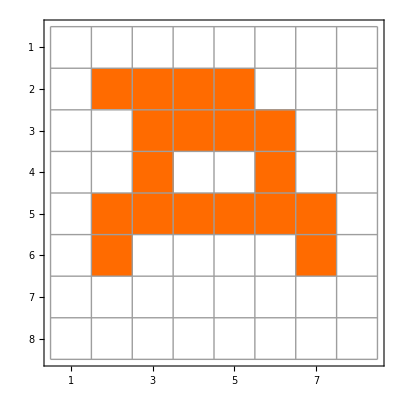

```mathematica
exSize := 8;
golData = 1 - ImageData[Binarize[ImageResize[Rasterize["A"],{exSize,exSize}]]];
MatrixPlot[golData, Mesh -> True]
```

Similarly as was previously done with Snakes and Ladders, we build up the constraint formula passed to SatisfiabilityInstances piecemeal from the propositions known to be true and false from the tiles in the given initial state (here at time 1), and the clauses that constrain the values of the unknown tiles at the next state (here at time 2).The answer is similarly extracted and decoded from the solution of truth values of all the propositions used to define this problem, one proposition per each tile and moment of time.

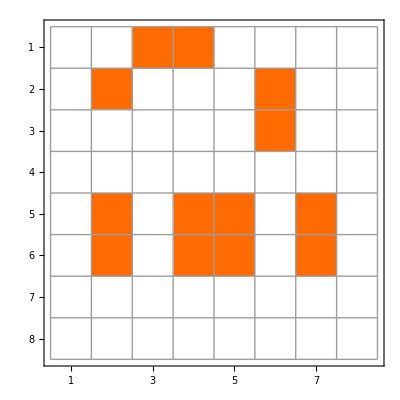

```mathematica
gol1 := golLiterals[1, exSize];
gol2 := golLiterals[2, exSize];
formula2 :=BooleanConvert[
And[
golEncode[golData, 1],
And @@ Flatten[Table[golClauses[x,y,2,exSize],{x,1,exSize},{y,1,exSize}],2]
],"CNF"];

golVars2 = Join[gol1, gol2];
golSol2 = First[SatisfiabilityInstances[formula2, golVars2 ]];
sols2 = Map[First,Cases[Transpose[{golVars2, golSol2}],{xx_,True}]];
MatrixPlot[golDecode[sols2, 2, exSize], Mesh -> True]
```

So far using propositional logic to compute the next step of Conway’s Game of Life has not been anything special, since unlike Sudoku that needs recursion to try out the possible values for each tile and backtracking whenever its forward checking mechanism realizes that it has painted itself in a corner because some tile has no more possible values remaining because its twenty neighbours have already used up all the values from 1 to 9, the evolution from the initial state of Conway’s Game of Life is rather trivial to compute forward any number of time steps with nested loop that loop over the time and the game board, which makes this problem easy enough to serve as an exercise in a first programming course. However, the propositional logic approach allows us to do something that would not be anywhere as trivial to solve using imperative programming; execute the rules backward in time so that given the initial state at time t, we wish to compute the previous state at time t - 1 that would generate the initial state if the forward rules of the game were applied to it!
In all programming languages, computational statements are intentionally designed so that the state of the system at time t + 1 is easy to compute from the given the state of the system at the previous time t.  However, unlike statements in programming languages, the propositional logic formulas that constrain the values of tiles between consecutive time steps are perfectly symmetric, so the previous satisfiability solver can be used, without any modification whatsoever to its structure, to solve the values of tiles at time t - 1 from their known values at the current time t.
There is one giant fly in this ointment, though. Even though the rules of the game are perfectly deterministic in the forward direction so that the initial state of the game fully determines all of its future states, even one googolplex steps ahead unimaginably far in the future, the same determinism does not hold when time moves in the reverse directions. The exact same state of Conway’s Game of Life at time t can be produced by many different states at time t - 1. In fact, it is easy to see that this problem always has a large number of solutions, typically exponentially many. For example, any individual tile inside some 3-by-3 area that is empty at time t could have just as well been dead or alive at time t - 1. Given only the current state of the game, it is impossible for us to tell which one of these result-equivalent states actually took place. On the other hand, it is also perfectly possible that no such previous state exists at all, because the current state is logically impossible to produce from any state using the rules of Conway’s Game of Life! (A trivial example of such an impossible state would be one whose every tile is alive.)
This introduction of exponential nondeterminism is inherent and unavoidable in all universal computation any time (heh) that we attempt to reverse the arrow of time to find out which particular input would produce the desired output. Since Conway’s Game of Life is computationally universal and Turing-complete, the same phenomenon will inevitably occur in our attempt to reverse that game. If all computations were mechanistically reversible, any encryption algorithm could be executed in reverse to work as its own decryption algorithm. More generally, any algorithm that checks whether the offered solution of some problem is a valid one could be run backwards to work as an algorithm that finds a solution to that particular problem! Countless other similar goodies, equivalents of having a Christmas every day from the computational point of view, would rain on humanity like endless manna from heavens.
The state of each tile at time t + 1 does not directly depend on the state of any of its neighbouring tiles at the time t + 1, but only on the known states of the neighbouring tiles at time t, which makes that state easy to compute looking only at the immediate neighbourhood. The same simplicity does not hold in backwards direction. Given the known states at time t + 1, the unknown state of each tile at time t is also constrained by the states of its eight neighbours at that same time t, whose states will then depend on their neighbours, and so on, so that every tile indirectly depends on every other tile at the same time! The satisfiability solver then has an exponentially harder row to hoe when it tries to build up a working global combination of tile values that simultaneously satisfies the given constraints. When time flow forward, the value of each time can be computed in complete isolation from the values of the tiles for the rest of the board, which allows this task in principle to be parallelized without limit so that each tile could be computed with a separate processor for blazingly fast generation of future states.
However, the logic of setting up the problem using our previous functions is exactly the same backwards as it was forward. The only difference is that the clauses now define how the known current state at time 1 depends on the unknown previous state at time 0, instead of how the unknown next state at time 2 deterministically depends on the known current state at time 1.

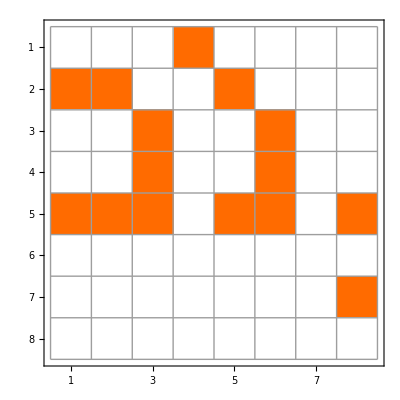

```mathematica
gol0 = golLiterals[0, exSize];
formula1 :=BooleanConvert[
And[
golEncode[golData, 1],
And @@ Flatten[Table[golClauses[x,y,1,exSize],{x,1,exSize},{y,1,exSize}],2]
],"CNF"];
golVars1 = Join[gol0, gol1];
golSol1 = First[SatisfiabilityInstances[formula1, golVars1 ]];
sols1 = Map[First,Cases[Transpose[{golVars1, golSol1}],{xx_,True}]];
MatrixPlot[golDecode[sols1, 0, exSize], Mesh -> True]
```

As the third example of reducing computational problems to propositional logic is Problem 215 of Project Euler, “Crack-Free Tilings”. The task is to fill a w-by-h wall using arbitrary 2-by-1 and 3-by-1 tiles, but under the constraint that there are no vertical cracks anywhere in this filling. The module crackFree converts this problem into symbols that say that a tile of length t has its top left corner in the given coordinates. The function noOverlap produces clauses to say no two tiles may overlap each other and that there may not be a crack. The function outside produces the clauses to say that no tile reaches outside this wall, and the function cover says that every square must be covered by some tile. The built-in function SatisfiabilityCount is used to tally the number of solutions that satisfy all these constraints, this number then being equal to the number of solutions to the original problem.

```mathematica
crackFreeClauses[w_,h_] := Module[{noOverlap, outside, cover, clauses, allClauses},
sym[x_,y_,t_] := If[1 ≤ x ≤ w && 1 ≤ y ≤ h, Subscript[s,{x,y,t}], False];
noOverlap[x_,y_] :=And @@ Join[
{
sym[x,y,2] ⇒ ¬(sym[x,y,3] ∨ sym[x+1,y,2] ∨ sym[x+1,y,3]),
sym[x,y,3]⇒¬( sym[x,y,2]∨ sym[x+1,y,2] ∨ sym[x+1,y,3] ∨ sym[x+2,y,2] ∨ sym[x+2,y,3])
},
If[x > 1 && y > 1,
{
(sym[x,y,2]⇒ ¬(sym[x,y-1,2] ∨ sym[x,y-1,3])) ∧
(sym[x,y,3]⇒  ¬(sym[x,y-1,2] ∨ sym[x,y-1,3]))
},
{True}]
];

outside[x_ /; x > w-1,y_ ] :=  ¬(sym[x,y,2] ∨ sym[x,y,3]);
outside[x_ /; x > w-2, y_] := ¬sym[x,y,3];
outside[x_, y_] := True;

cover[x_,y_] := If[1≤x ≤ w && 1≤ y ≤ h,
sym[x,y,2] ∨ sym[x,y,3] ∨ sym[x-1,y,2] ∨ sym[x-1,y,3] ∨ sym[x-2,y,3],
True
];

clauses[x_,y_] := noOverlap[x,y] ∧ outside[x,y] ∧ cover[x,y];

allClauses = And @@Flatten[Table[clauses[x,y],{x,1,w},{y,1,h}],2];
BooleanConvert[allClauses, "CNF"]
];

c10by3 = crackFreeClauses[10, 3];
SatisfiabilityCount[c10by3, BooleanVariables[c10by3]]
```

12

Converting the solution found by this logic to graphical display for humans should be pretty straightforward by now. To create a more interesting solution to display here than the first solution that uses mainly 3-by-1 tiles to avoid violating the constraints, we impose a couple of additional conditions that force the solution to contain some 2-by-1 tiles in the internal positions.

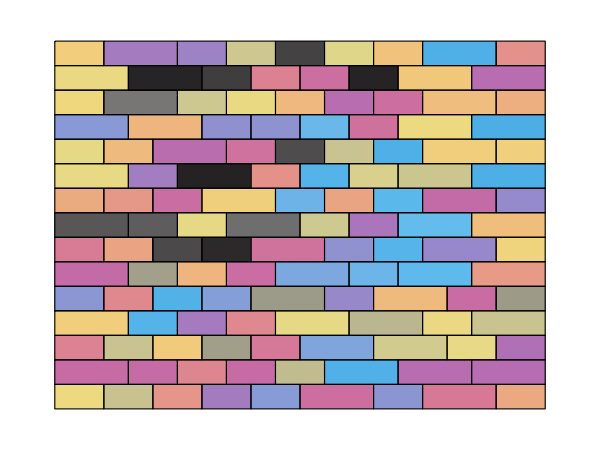

```mathematica
tile[Subscript[s,{x_,y_,t_}],cf_] := {cf[RandomReal[]],Polygon[{{x,y},{x+t,y},{x+t,y-1},{x,y-1}}]};
wall[literals_] := With[{cf = ColorData["CMYKColors"]},Graphics[{
EdgeForm[{Thick, Black}],
Table[tile[lit,cf], {lit, literals}]
}, ImageSize ->   600]];
clauses = crackFreeClauses[20,15] ∧ Subscript[s,{10,2,2}] ∧ Subscript[s,{14,7,2}];
vars = BooleanVariables[clauses];
instances = SatisfiabilityInstances[clauses, vars];
sol = instances[[1]];
wall[Map[First, Cases[Transpose[{vars, sol}], {x_, True}]]]
```

The number of clauses produced quickly makes this problem infeasible for the satisfiability solver of Mathematica. However, this same problem can be solved more efficiently in dynamic programming spirit by using memoization of the recursion that adds up the solutions. The recursion that counts the number of ways to solve this problem fills in the tiles of the current row from the current loc-ation. It has the base cases of the entire wall being filled, in which case there is exactly one way to complete the job by doing nothing and declaring victory, and the current row having become impossible to complete. Otherwise, if the recursion has managed to completely fill in the current row without creating a crack with the previous row, the positions of the cracks in the current row become the cracks of the row positioned below the current row for the next level of recursion. To avoid the exponential blowup of this recursion, the repeated subproblems are automatically memoized using the canonical “Lazy assignment of eager assignments” idiom of Mathematica.

```mathematica
tilings[w_,ht_, bricks_:{2,3}] := Module[{ways},
ways[0,loc_,below_,left_] := 1;
ways[h_,loc_ /; loc == 0 || MemberQ[bricks, loc], below_,left_] := 
ways[h,loc,below, left] = ways[h-1, w, left, {}];

ways[h_,loc_ /; loc < 0 ||loc == 1, below_, left_] := 0;

ways[h_,loc_, below_,left_] :=ways[h,loc,below, left] =
Total[
Table[
If[loc > b && MemberQ[ below, loc-b],0,ways[h, loc - b, below, Join[{loc-b}, left] ]
], {b, bricks}]
];
ways[ht,w,{},{}]
];
```

We can tabulate the answers to this problem for a w-by-10 wall reasonably quickly, with w going through the values from 3 to 25. Note how this problem has no solutions when w equals 4, since there is no way not to leave a crack using only tiles of length 2. The walls of length from 5 to 7 have only two solutions regardless of the height, since the placement of the tiles on the first row will determine their placements in the entire wall. As w increases from there, the number of possible tilings suddenly shoots up exponentially.

```mathematica
Table[tilings[w,10], {w, 3, 25}]
```

{1,0,2,2,2,4,66,290,652,1586,9594,45358,142704,419854,1778422,7939970,28421942,94082988,360133872,1478534470,5578404294,19730715436,73368404198}

Increasing the height of the wall by just one has a dramatic effect on the number of solutions. Combinatorics is the stuff of many possibilities, and yet the answers will always be integers as the Good Lord intended for us extreme finitists.

```mathematica
Table[tilings[w,11], {w, 3, 25}]
```

{1,0,2,2,2,4,98,468,1138,2954,20932,121056,407878,1282068,6484448,32698220,135084042,482666366,2051365490,10094853172,41983996110,166491260832,698163645734}

Just out of curiosity, can Mathematica find some simple function that fits this pattern? Nah.

```mathematica
FindSequenceFunction[%]
```

FindSequenceFunction[{1,0,2,2,2,4,98,468,1138,2954,20932,121056,407878,1282068,6484448,32698220,135084042,482666366,2051365490,10094853172,41983996110,166491260832,698163645734}]

To score the achievement point for Project Euler, we need to solve the particular larger instance that was required in the problem. This computation takes a little while in Mathematica, especially when contrasted to the fact that the author’s implementation of the exact same memoized recursion in Python 3 takes about one second to execute in the author’s trusty old desktop machine. On the other hand, that Python 3 solution has to memoize only tuples of integers instead of arbitrary expressions. The resulting solution of there existing about 806 trillion different possibilities to fill in the 32-by-10 wall without cracks is accepted by Project Euler.

```mathematica
Timing[tilings[32,10]]
```

{45.48231,806844323190414}